```mathematica
fcogs ={};
nus={};
AESs={};
BESs={};
AE153s={};
BE153s={};
scanUps={};
scanDowns={};
```

## Voltage Systematics

```mathematica
fittedDirectory = "C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=5-2\\2022-06-21 Voltage\\fit_result"
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=5-2\2022-06-21 Voltage\fit_result

```mathematica
SetDirectory[fittedDirectory]
voltages =FileNames["V*fit.csv"];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=5-2\2022-06-21 Voltage\fit_result

```mathematica
vs ={};
fcogvs ={};
gammas={};
nuvs={};
AESvs={};
BESvs={};
AE153vs={};
BE153vs={};

For[i=1,i≤Length[voltages],i++,
voltageFit = Import[voltages[[i]]];
v=Around[voltageFit[[2,2]],voltageFit[[3,2]]];
fcogv = Around[voltageFit[[2,3]],voltageFit[[3,3]]];
gammav = Around[voltageFit[[2,4]],voltageFit[[3,4]]];
nuv = Around[voltageFit[[2,5]],voltageFit[[3,5]]];
AESv = Around[voltageFit[[2,6]],voltageFit[[3,6]]];
BESv = Around[voltageFit[[2,7]],voltageFit[[3,7]]];
BE153v = Around[voltageFit[[2,8]],voltageFit[[3,8]]];
AE153v = Around[voltageFit[[2,9]],voltageFit[[3,9]]];

AppendTo[vs,v];
AppendTo[fcogvs,fcogv];
AppendTo[gammas,gammav];
AppendTo[nuvs,nuv];
AppendTo[AESvs,AESv];
AppendTo[BESvs,BESv];
AppendTo[AE153vs,AE153v];
AppendTo[BE153vs,BE153v];

AppendTo[fcogs,voltageFit[[All,3]]];AppendTo[nus,voltageFit[[All,5]]];
AppendTo[AESs,voltageFit[[All,6]]];
AppendTo[BESs,voltageFit[[All,7]]];
AppendTo[BE153s,voltageFit[[All,8]]];
AppendTo[AE153s,voltageFit[[All,9]]];
AppendTo[scanUps,voltageFit[[All,3]][[4;;7]]];
AppendTo[scanDowns,voltageFit[[All,3]][[8;;]]];
]
```

FittedModel[3571.31+0.000260705 x]

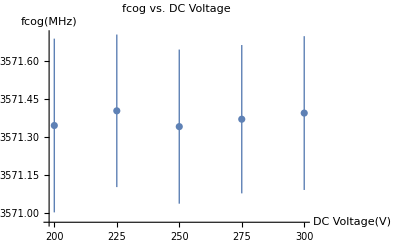

0.134564

```mathematica
lmv = LinearModelFit[Transpose[{vs,fcogvs[[All,1]]}],x,x]
Show[ListPlot[Transpose[{vs,fcogvs}],PlotRange->All,AxesLabel->{"DC Voltage(V)","fcog(MHz)"},PlotLabel->"fcog vs. DC Voltage"](*,Plot[lmv[x],{x,200,350}]*)]
lmv["RSquared"]
```

```mathematica
AESvs
```

{-157.020.05,-157.030.04,-157.040.04,-157.040.04,-157.040.04}

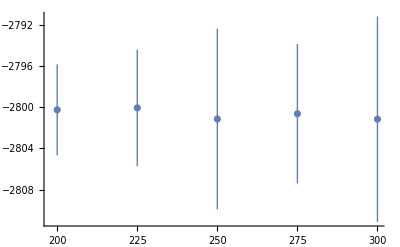

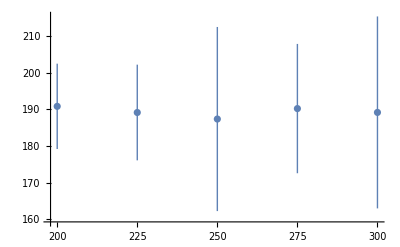

```mathematica
(*ListPlot[Transpose[{vs,gammas}],PlotRange->All]*)
ListPlot[Transpose[{vs,nuvs}],PlotRange->All]
ListPlot[Transpose[{vs,BE153vs}],PlotRange->All]
```

```mathematica
meansV ={Mean[fcogvs],Mean[gammas],Mean[nuvs]}
```

{3571.370.14,41.8912(√(^2))/(√5),-2800.63.3}

## Pressure Systematics

```mathematica
directoryPressure ="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=5-2\\2022-06-22 Pressure\\fitResult";
SetDirectory[directoryPressure]
pressures =FileNames["P*fit.csv"];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=5-2\2022-06-22 Pressure\fitResult

```mathematica
ps ={};
fcogps ={};
gammas={};
nups={};
AESps={};
BESps={};
AE153ps={};
BE153ps={};

For[i=1,i≤Length[pressures],i++,
pressureFit = Import[pressures[[i]]];
p=Around[pressureFit[[2,2]],pressureFit[[3,2]]];
fcogp = Around[pressureFit[[2,3]],pressureFit[[3,3]]];
gammap = Around[pressureFit[[2,4]],pressureFit[[3,4]]];
nup = Around[pressureFit[[2,5]],pressureFit[[3,5]]];
AESp = Around[pressureFit[[2,6]],pressureFit[[3,6]]];
BESp = Around[pressureFit[[2,7]],pressureFit[[3,7]]];
BE153p = Around[pressureFit[[2,8]],pressureFit[[3,8]]];
AE153p = Around[pressureFit[[2,9]],pressureFit[[3,9]]];

AppendTo[ps,p];
AppendTo[fcogps,fcogp];
AppendTo[gammas,gammap];
AppendTo[nups,nup];
AppendTo[AESps,AESp];
AppendTo[BESps,BESp];
AppendTo[AE153ps,AE153p];
AppendTo[BE153ps,BE153p];

AppendTo[fcogs,pressureFit[[All,3]]];AppendTo[nus,pressureFit[[All,5]]];
AppendTo[AESs,pressureFit[[All,6]]];
AppendTo[BESs,pressureFit[[All,7]]];
AppendTo[BE153s,pressureFit[[All,8]]];
AppendTo[AE153s,pressureFit[[All,9]]];
If[i==2,
AppendTo[scanUps,pressureFit[[All,3]][[4;;7]]];
AppendTo[scanDowns,pressureFit[[All,3]][[8;;]]];]
]
```

FittedModel[3573.6-0.00859376 x]

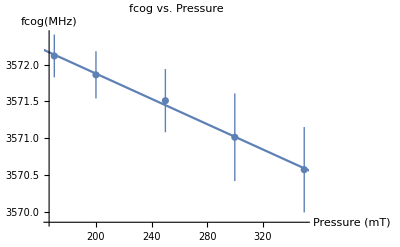

0.996984

```mathematica
lmp = LinearModelFit[Transpose[{ps,fcogps[[All,1]]}],x,x]
Show[ListPlot[Transpose[{ps,fcogps}],PlotRange->All,AxesLabel->{"Pressure (mT)","fcog(MHz)"},PlotLabel->"fcog vs. Pressure"],Plot[lmp[x],{x,150,400}]]
lmp["RSquared"]
```

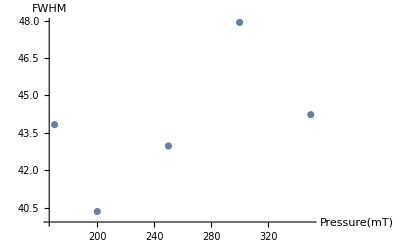

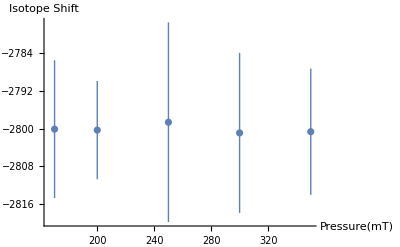

```mathematica
ListPlot[Transpose[{ps,gammas}],PlotRange->All,AxesLabel->{"Pressure(mT)","FWHM"}]
ListPlot[Transpose[{ps,nups}],PlotRange->All,AxesLabel->{"Pressure(mT)","Isotope Shift"}]
```

```mathematica
meansP ={Mean[fcogps],Mean[nups]}
```

{3571.410.21,-2800.7.}

## Power Systematics

```mathematica
directoryI="C:\\Users\\maruk\\Desktop\\Research\\PHY242\\retake\\Europium J=5-2\\2022-06-21 Laser Power\\fit_result";
SetDirectory[directoryI]
intensities =FileNames["s*fit.csv"];
```

C:\Users\maruk\Desktop\Research\PHY242\retake\Europium J=5-2\2022-06-21 Laser Power\fit_result

```mathematica
ints ={};
fcogints ={};
gammas={};
nuints={};
AESints={};
BESints={};
AE153ints={};
BE153ints={};

For[i=1,i≤Length[intensities],i++,
intensityFit = Import[intensities[[i]]];
int=Around[intensityFit[[2,2]],intensityFit[[3,2]]];
fcogint = Around[intensityFit[[2,3]],intensityFit[[3,3]]];
gammaint = Around[intensityFit[[2,4]],intensityFit[[3,4]]];
nuint = Around[intensityFit[[2,5]],intensityFit[[3,5]]];
AESint = Around[intensityFit[[2,6]],intensityFit[[3,6]]];
BESint = Around[intensityFit[[2,7]],intensityFit[[3,7]]];
BE153int = Around[intensityFit[[2,8]],intensityFit[[3,8]]];
AE153int = Around[intensityFit[[2,9]],intensityFit[[3,9]]];

AppendTo[ints,int];
AppendTo[fcogints,fcogint];
AppendTo[gammas,gammaint];
AppendTo[nuints,nuint];
AppendTo[AESints,AESint];
AppendTo[BESints,BESint];
AppendTo[AE153ints,AE153int];
AppendTo[BE153ints,BE153int];

AppendTo[fcogs,intensityFit[[All,3]]];AppendTo[nus,intensityFit[[All,5]]];
AppendTo[AESs,intensityFit[[All,6]]];
AppendTo[BESs,intensityFit[[All,7]]];
AppendTo[BE153s,intensityFit[[All,8]]];
AppendTo[AE153s,intensityFit[[All,9]]];
AppendTo[scanUps,intensityFit[[All,3]][[4;;7]]];
AppendTo[scanDowns,intensityFit[[All,3]][[8;;]]];
]
```

FittedModel[3571.11+0.109014 x]

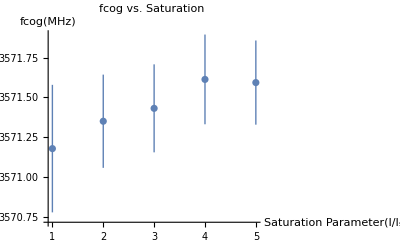

0.9196

```mathematica
lmi = LinearModelFit[Transpose[{ints,fcogints[[All,1]]}],x,x]
Show[ListPlot[Transpose[{ints,fcogints}],PlotRange->All,AxesLabel->{"Saturation Parameter(I/I_s)","fcog(MHz)"},PlotLabel->"fcog vs. Saturation"],Plot[lmi[x],{x,150,350}]]
lmi["RSquared"]
```

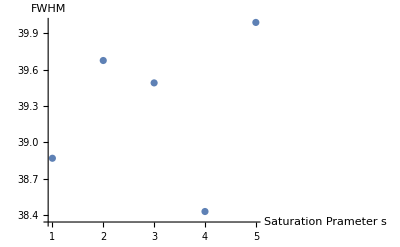

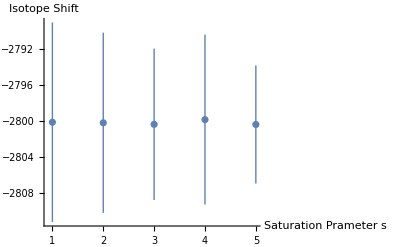

```mathematica
ListPlot[Transpose[{ints,gammas}],PlotRange->All,AxesLabel->{"Saturation Prameter s","FWHM"}]
ListPlot[Transpose[{ints,nuints}],PlotRange->All,AxesLabel->{"Saturation Prameter s","Isotope Shift"}]
```

```mathematica
meansP ={Mean[fcogints],Mean[nuints]}
```

{3571.430.14,-2800.4.}

```mathematica
5146+652384520
```

652389666

```mathematica
Mean[Join[nuvs[[All]],nups[[All]],nuints[[All]]]]
```

-2800.32.9

```mathematica
Mean[Join[fcogints,fcogps,fcogvs]]
```

3571.410.09

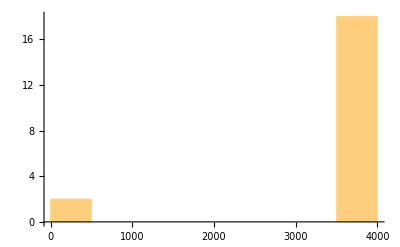

```mathematica
Histogram[Flatten[{voltageFit[[All,3]],intensityFit[[All,3]]}],11]
```

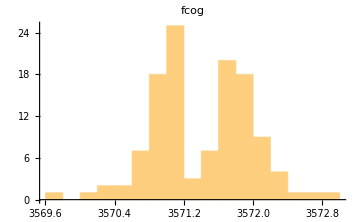

```mathematica
histFcog=Histogram[Flatten[fcogs[[All,4;;]]],11,PlotLabel->"fcog",ImageSize->Medium]
```

```mathematica
flattenedUps=Flatten[scanUps];
flattenDowns=Flatten[scanDowns];
```

```mathematica
shifts=Table[(flattenedUps[[n]]-flattenDowns[[n]])/2,{n,1,Length[flattenDowns]}];
shiftedUp=flattenedUps-shifts;
shiftedDown=flattenDowns+shifts;
```

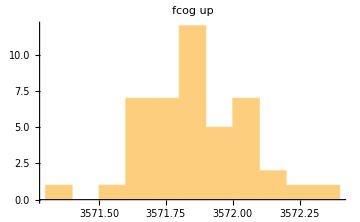

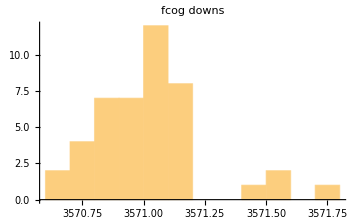

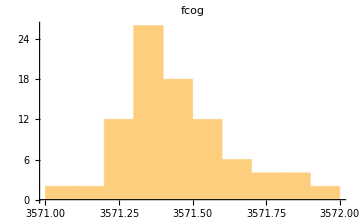

```mathematica
shift=(Mean[Flatten[scanUps]]-Mean[Flatten[scanDowns]])/2;

Histogram[flattenedUps,10,PlotLabel->"fcog up",ImageSize->Medium]
Histogram[flattenDowns,10,PlotLabel->"fcog downs",ImageSize->Medium]
fcogShifted=Histogram[Join[shiftedUp,shiftedDown],10,PlotLabel->"fcog",ImageSize->Medium]
```

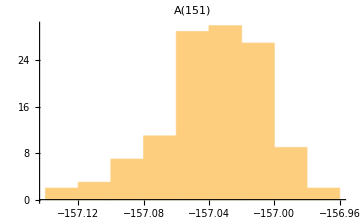

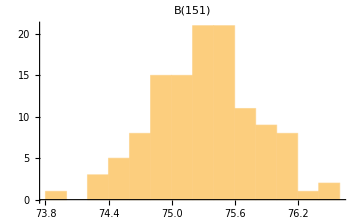

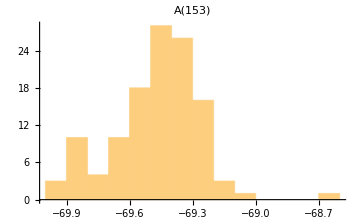

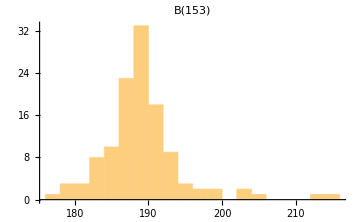

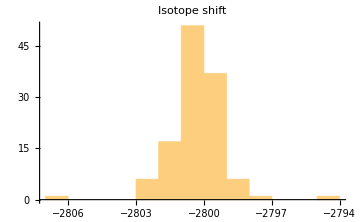

```mathematica
histA151=Histogram[Flatten[AESs[[All,4;;]]],11,PlotLabel->"A(151)",ImageSize->Medium]
histB151=Histogram[Flatten[BESs[[All,4;;]]],11,PlotLabel->"B(151)",ImageSize->Medium]
histA5153=Histogram[Flatten[AE153s[[All,4;;]]],15,PlotLabel->"A(153)",ImageSize->Medium]
histB153=Histogram[Flatten[BE153s[[All,4;;]]],15,PlotLabel->"B(153)",ImageSize->Medium]
histIso=Histogram[Flatten[nus[[All,4;;]]],15,PlotLabel->"Isotope shift",ImageSize->Medium]
```

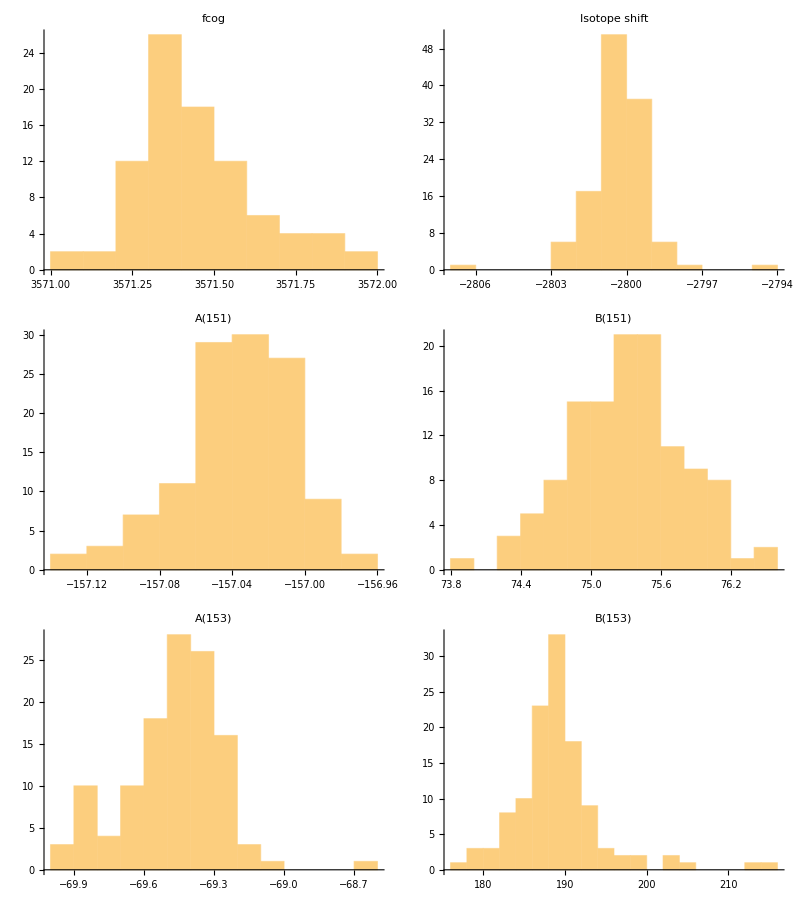

```mathematica
Grid[{{fcogShifted,histIso},{histA151,histB151},{histA5153,histB153}}]
```

```mathematica
fogerror=Max[{Mean[fcogs[[All,3]]],
StandardDeviation[Flatten[fcogs[[All,4;;]]]]}];
AESerror=Max[{Mean[AESs[[All,3]]],
StandardDeviation[Flatten[AESs[[All,4;;]]]]}];
BESerror=Max[{Mean[BESs[[All,3]]],
StandardDeviation[Flatten[BESs[[All,4;;]]]]}];
AE153error=Max[{Mean[AE153s[[All,3]]],
StandardDeviation[Flatten[AESs[[All,4;;]]]]}];
BE153error=Max[{Mean[BE153s[[All,3]]],
StandardDeviation[Flatten[BESs[[All,4;;]]]]}];
```

```mathematica
result = {{Mean[Flatten[fcogs[[All,4;;]]]],fogerror},{Mean[Flatten[AESs[[All,4;;]]]],AESerror},{Mean[Flatten[BESs[[All,4;;]]]], BESError},{Mean[Flatten[AE153s[[All,4;;]]]],AE153error},{Mean[Flatten[BE153s[[All,4;;]]]], BE153error}};
TableForm[result,TableHeadings->{{"fcog","AES","BES","AE153","BE153"},{"Mean","error"}}]
```

| Mean | error
fcog | 3571.41 | 0.554978
AES | -157.037 | 0.0478433
BES | 75.3045 | 0.972509
AE153 | -69.4687 | 1.70167
BE153 | 189.11 | 25.5401

-Graphics-

```mathematica
voltages//TableForm
```

V200fit.csv
V225fit.csv
V250fit.csv
V275fit.csv
V300fit.csv

```mathematica
num=2;
Join[{Join[{"","Mean value","error"},Table["",{n,1,Length[fcogResult]}]]},{Flatten[{"Voltage",voltage,voltageError,Table[voltage,{n,1,Length[fcogResult]}]}],fcogs[[num]],gammas,nus[[num]],AESs[[num]],BESs[[num]],BE153s[[num]],AE153s[[num]]}]
```

{{,Mean value,error,,,,,,,,},{Voltage,200,0,200,200,200,200,200,200,200,200},{fcog,3571.4,0.301208,3571.87,3571.86,3571.81,3571.7,3571.03,3571.09,3570.89,3570.99},{38.8677,39.6764,39.4911,38.4271,39.9913},{isotope shift,-2800.05,5.67195,-2800.33,-2799.65,-2799.88,-2801.25,-2799.76,-2799.53,-2799.7,-2800.3},{AES,-157.033,0.0426699,-157.041,-157.019,-157.016,-157.059,-157.042,-157.042,-157.02,-157.023},{BES,75.382,0.919925,74.8965,74.9869,75.2585,75.875,75.6623,75.2145,75.5972,75.5655},{BE153,189.145,13.0788,188.916,190.204,189.8,192.726,187.726,187.358,188.618,187.812},{AE153,-69.4216,1.07882,-69.5078,-69.4393,-69.4302,-69.3225,-69.4466,-69.5039,-69.3864,-69.3359}}

```mathematica
voltageFit[[All]]//TableForm
```

| Pressure | fcog | gamma | isotope shift | AES | BES | BE153 | AE153
Mean value | 300 | 3571.4 | 41.1281 | -2801.15 | -157.043 | 75.2044 | 189.165 | -69.2929
error | 0 | 0.303656 |  | 10.0016 | 0.0392562 | 0.921224 | 26.2374 | 1.26832
 | 300 | 3571.63 | 42.458 | -2802.02 | -156.999 | 75.1523 | 192.646 | -69.3366
 | 300 | 3571.89 | 42.2865 | -2801.51 | -157.05 | 75.4329 | 188.323 | -69.132
 | 300 | 3572.02 | 43.5447 | -2800.3 | -157.051 | 75.3642 | 188.513 | -69.2849
 | 300 | 3571.72 | 43.0882 | -2800.69 | -157.013 | 75.3805 | 189.891 | -69.3187
 | 300 | 3570.99 | 42.0789 | -2800.21 | -157.073 | 76.1159 | 189.124 | -69.3349
 | 300 | 3571.13 | 39.818 | -2802.53 | -157.006 | 73.9543 | 190.654 | -69.0532
 | 300 | 3570.81 | 37.3503 | -2800.64 | -157.102 | 75.7344 | 186.506 | -69.2781
 | 300 | 3570.98 | 38.4005 | -2801.31 | -157.052 | 74.5011 | 187.667 | -69.6047